```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
pathSRC="../../src/";
Get[pathSRC<>"basic.m"]
Get[pathSRC<>"negf.m"]
Get[pathSRC<>"dftb.m"]
Get[pathSRC<>"xyz.m"]
Get["../../skf/auorg.E.m"]
Get["../../skf/auorg.V.mx"]
Get["../../skf/auorg.S.mx"]
```

-17.1434

## Geo & Ham

```mathematica
structName="mcpp_jt";
{atoms0,types0,bonds0}=ImportXYZ[structName~~".xyz"];
```

```mathematica
NL=75;NR=75;NC=Length[types0]-2NL-2NR;
{atomsL2,atomsL,atomsC,atomsR,atomsR2}=TakeList[atoms0,{NL,NL,NC,NR,NR}];
{typesL2,typesL,typesC,typesR,typesR2}=TakeList[types0,{NL,NL,NC,NR,NR}];
NATOM=Length[atomsC];
```

```mathematica
HC=DFTBSolver2[atomsC,typesC];
HL=DFTBSolver2[atomsL,typesL];
HR=DFTBSolver2[atomsR,typesR];
HCL=CalcV12[{atomsC,typesC},{atomsL,typesL}];
HCR=CalcV12[{atomsC,typesC},{atomsR,typesR}];
HL01=CalcV12[{atomsL,typesL},{atomsL2,typesL2}];
HR01=CalcV12[{atomsR,typesR},{atomsR2,typesR2}];

NO=Length[HC];
SC=DFTBSolverOver[atomsC,typesC];
SL=DFTBSolverOver[atomsL,typesL];
SR=DFTBSolverOver[atomsR,typesR];
SCL=CalcS12[{atomsC,typesC},{atomsL,typesL}];
SCR=CalcS12[{atomsC,typesC},{atomsR,typesR}];
SL01=CalcS12[{atomsL,typesL},{atomsL2,typesL2}];
SR01=CalcS12[{atomsR,typesR},{atomsL2,typesR2}];
```

```mathematica
h=DFTBSolver2[atomsC,typesC];
s=DFTBSolver2[atomsC,typesC,"S"];
{eval,evec}=MyEigensystem[{h,s}];
{EHOMO,ELUMO,EF,Egap,NHOMO}=GetHOLU[eval,evec,atomsC,typesC]
```

{-4.83001,-4.76994,-4.79998,0.0600748,481}

```mathematica
coordForOrb=Table[Table[atoms⟦i⟧,{MAXORB[types⟦i⟧]}],{i,Length[types]}]~Flatten~1;
```

## Electronic Structure

```mathematica
HC//Dimensions
```

{822,822}

```mathematica
atomsC//Length
```

136

```mathematica
eval[[NHOMO+{0,1}]]
```

{-4.83001,-4.76994}

-4.79998

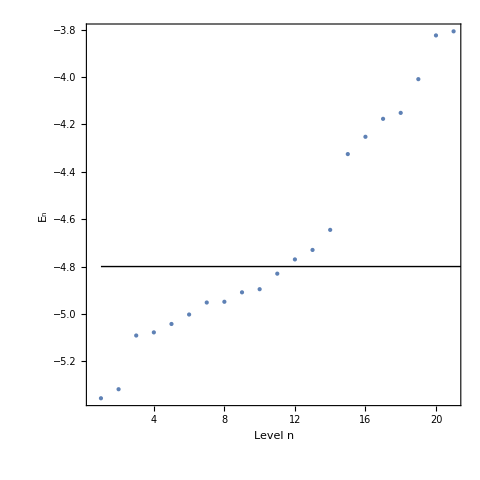

```mathematica
setEF=eval[[NHOMO+{0,1}]]//Mean
Show[
ListPlot[eval[[NHOMO-10;;NHOMO+10]],PlotRange->{All,All},styles,
FrameLabel->{"Level n","E_n"}
],
Plot[setEF,{x,1,NO},PlotStyle->{Black,Thick}]
]
```

## Elctrode

```mathematica
Table[
(*setEF=-3.9;*)
η=1*^-7;

tL=HL01-setEF SL01;
tR=HR01-setEF SR01;
tCL=HCL-setEF SCL;
tCR=HCR-setEF SCR;

GL=CalcSurGS[setEF,HL,tL,tL†,SL];
GR=CalcSurGS[setEF,HR,tR,tR†,SR];
ΣL=tCL.GL.tCL†//SparseArray;
ΣR=tCR.GR.tCR†//SparseArray;
{ΓL,ΓR}=-2Im/@{ΣL,ΣR};
ΣL>>"SigmaL-S1-"<>ToString[-setEF*10//Rationalize]<>".m";
ΣR>>"SigmaR-S1-"<>ToString[-setEF*10//Rationalize]<>".m";
Null,
{setEF,-4.8,-4.8,0.1}
]
```

{Null}